# Visualization of the Robustness and Flexibility of Evolved SL Walkers

### Global Definitions

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Walker Animation Parameters

```mathematica
$Head={{29.4,0},{21.9,11.25},{14.4,0},{21.9,-11.25},{29.4,0}};$Torso={{18,6},{0,12},{-30,5},{-30,-5},{0,-12},{18,-6}};$LeftAnt={{25.65,-5.6},{65,-20}};$RightAnt={{25.65,5.6},{65,20}};$LeftCercus={{-30,-2},{-34,-8}};$RightCercus={{-30,2},{-34,8}};
```

```mathematica
DisplayBody[{JointX_,JointY_,FootX_,FootY_,FootState_}]:=
Module[{Head,Torso,LeftAnt,RightAnt,LeftCercus,RightCercus,Leg,Foot},
Head=Map[{#⟦1⟧+JointX,#⟦2⟧}&,$Head];
Torso=Map[{#⟦1⟧+JointX,#⟦2⟧}&,$Torso];
LeftAnt=Map[{#⟦1⟧+JointX,#⟦2⟧}&,$LeftAnt];
RightAnt=Map[{#⟦1⟧+JointX,#⟦2⟧}&,$RightAnt];
LeftCercus=Map[{#⟦1⟧+JointX,#⟦2⟧}&,$LeftCercus];
RightCercus=Map[{#⟦1⟧+JointX,#⟦2⟧}&,$RightCercus];
Leg={{JointX,JointY},{FootX,FootY}}; 
Foot={FootX,FootY};
Show[
Graphics[
{{RGBColor[1,0.6,0],Polygon[Head],Polygon[Torso]},{RGBColor[0.6, 0.4, 0.2],Line[LeftAnt],Line[RightAnt],Line[LeftCercus],Line[RightCercus],Line[Head],Line[Torso],Thickness[0.005]},{RGBColor[0.6, 0.4, 0.2],Line[Leg],Thickness[0.05]},If[FootState==1,{RGBColor[0.6, 0.4, 0.2],PointSize[0.01],Point[Foot]},{}]}],AspectRatio->2/11,PlotRange->{{-35,550},{-50,50}}, ImageSize->Large,Frame->True,FrameTicks->{False,False}]]
```

### Data Import

```mathematica
Bodyts = Import["./src_tworeparam/body_ts.dat"];
NMts = Import["./src_tworeparam/nm_ts.dat"];
Tts = Import["./src_tworeparam/t_ts.dat"];
Paramsts = Import["./src_tworeparam/param_ts.dat"];
```

#### Derive Slider Ranges from Data

```mathematica
NMmin = Min[NMts]
NMmax = Max[NMts];
(*NMmax = 1*)
Tmin = Min[Tts]
(*Tmax = 1*)
Tmax = Max[Tts];
```

-0.63

-1

### Display Whole Figure

```mathematica
DisplayFigure[{JointX_,JointY_,FootX_,FootY_,FootState_},{bias1_,bias2_,bias3_,w11_,w12_,w13_,w21_,w22_,w23_,w31_,w32_,w33_},{T_},{C_}]:=
	Module[{Head,Torso,LeftAnt,RightAnt,LeftCercus,RightCercus,Leg,Foot},
	Head=Map[{#⟦1⟧+JointX,#⟦2⟧}&,$Head];
	Torso=Map[{#⟦1⟧+JointX,#⟦2⟧}&,$Torso];
	LeftAnt=Map[{#⟦1⟧+JointX,#⟦2⟧}&,$LeftAnt];
	RightAnt=Map[{#⟦1⟧+JointX,#⟦2⟧}&,$RightAnt];
	LeftCercus=Map[{#⟦1⟧+JointX,#⟦2⟧}&,$LeftCercus];
	RightCercus=Map[{#⟦1⟧+JointX,#⟦2⟧}&,$RightCercus];
	Leg={{JointX,JointY},{FootX,FootY}}; 
	Foot={FootX,FootY};
	Show[
	Graphics[
	{{RGBColor["#a288a6"],Polygon[Head],Polygon[Torso]},{Darker[RGBColor["#a288a6"]],Line[LeftAnt],Line[RightAnt],Line[LeftCercus],Line[RightCercus],
	Line[Head],Line[Torso],Thickness[0.005]},{Darker[RGBColor["#a288a6"]],Line[Leg],Thickness[0.05]},
	If[FootState==1,{Darker[RGBColor["#a288a6"]],PointSize[0.01],Point[Foot]},{}](*,
	Inset[Labeled[Slider[(T-Tmin)/(Tmax-Tmin),ImageSize->Small],"T",Left],{405,63}],Inset[Labeled[Slider[(C-NMmin)/(NMmax-NMmin),ImageSize->Small],"C",Left],{405,48}],
	Inset[BarChart[{bias1,bias2,bias3,w11,w12,w13,w21,w22,w23,w31,w32,w33},ChartLabels->{{"b1","b2","b3","w11","w12","w13","w21","w22","w23","w31","w32","w33"},{""}}
	,PlotRange->{Automatic,{-35,35}},Ticks->{{},{-30,-20,0,20,30}},ImageSize->Small,AspectRatio->1/3],{360,-30}]*)}],
	(*AspectRatio->1/6,PlotRange->{{-400,500},{-75,75}}, 
	ImageSize->Large,Frame->False,FrameTicks->{False,False}]*)
	AspectRatio->1/10,PlotRange->{{-35,565},{-30,30}}, 
	ImageSize->Large,Frame->False,FrameTicks->{False,False}]]
```

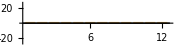

```mathematica
T = Import["/Users/LJSbo/Documents/School/Research/GitHub/Variability_Feedback_Walker/cpg4_body.dat"];
DisplayFigure[T[[1]],{1,1,1,1,1,1,1,1,1,1,1,1},0,0]
```

```mathematica
gif = Animate[DisplayFigure[Bodyts[[i]],Paramsts[[i]],Tts[[i]],NMts[[i]]],{i,1,Length[Bodyts],1}];
gif
```

```mathematica
Export["animation.mp4",gif]
```

General::sysffmpeg: Using a limited version of FFmpeg. Install FFmpeg to get more complete codec support.

animation.mp4

```mathematica
Export["slowanimation.mp4",gif,"DisplayDurations" -> 1]
```

slowanimation.mp4